```mathematica
Map[First,Tally[TrianglesWithPattern[7,1],PartitionType[#1]==PartitionType[#2]&]]
```

{{{1,3},{2,4},{5,7},{6}},{{1,3,7},{2,4},{5},{6}}}

```mathematica
PartitionType[{{1,3,7},{2,4},{5},{6}}]
```

{3,2,1,1}

```mathematica
ShowForNodesSHort[nodes_]:=Map[CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[#]]},
Join[EdgeList[g],VertexList[EdgeList[g]]]],GraphHighlightStyle->"Thick",VertexLabels->"Name"]&,Map[First,Tally[TrianglesWithPattern[nodes,1],PartitionType[#1]==PartitionType[#2]&]]]
```

```mathematica
ShowForNodes[nodes_,type_:1]:=Map[Labeled[CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[#]]},
Join[EdgeList[g],VertexList[EdgeList[g]]]],GraphHighlightStyle->"Thick",VertexLabels->"Name"],PartitionType[#]]&,TrianglesWithPattern[nodes,type]]
```

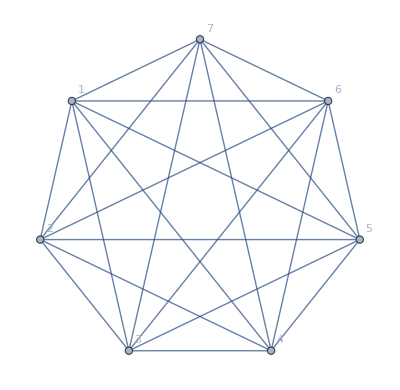
{-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{3,2,1,1},-Graphics-{3,2,1,1},-Graphics-{3,2,1,1},-Graphics-{3,2,1,1}}

```mathematica
ShowForNodes[7,1]
```

```mathematica
ShowForNodes[7,2]
```

{-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{3,2,1,1},-Graphics-{3,2,1,1},-Graphics-{3,2,1,1},-Graphics-{3,2,1,1}}

```mathematica
ShowForNodes[8,3]
```

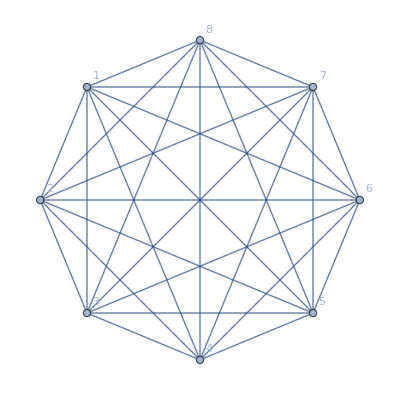
```mathematica
{-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},ShowForNodesFull{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1}}
```

```mathematica
ShowForNodesQuad[nodes_,type_:1]:=Map[Labeled[CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[#]]},
Join[EdgeList[g],VertexList[EdgeList[g]]]],VertexLabels->"Name"],PartitionType[#]]&,QuadrilateralsWithPattern[nodes,type]]
```

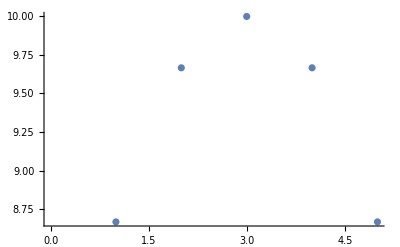

```mathematica
With[{nodes=10},Table[10-((i-6-(nodes-6)/2)^2/3),{i,6,nodes}]]//ListPlot
```

```mathematica
CoordinatesForNodes[nodes_]:=Table[{If[i≤5,i,i-(nodes/2)]*2,If[i≤5,((i-3)^2/3),10-((i-6-(nodes-6)/2)^2/3)]},{i,1,nodes}]
```

```mathematica
ShowForNodesQuad[nodes_,type_:1]:=Map[Labeled[Graph[Range[nodes],EdgeList[GraphComplement[GraphFromSets[#]]],GraphHighlightStyle->"Thick",VertexLabels->"Name",EdgeStyle->Red,VertexStyle->Green,VertexCoordinates->Table[{If[i≤5,i,i-(nodes/2)]*2,If[i≤5,((i-3)^2/3),10-((i-6-(nodes-6)/2)^2/3)]},{i,1,nodes}]],PartitionType[#]]&,QuadrilateralsWithPattern[nodes,type]]
```

```mathematica
QuadrilateralPattern[1]
```

{{1,3},{2},{4},{5}}

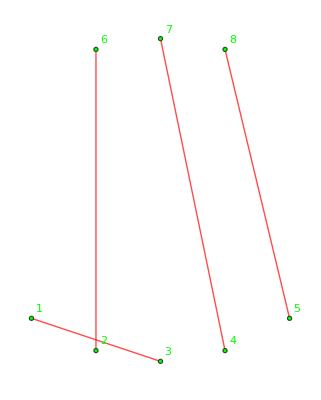
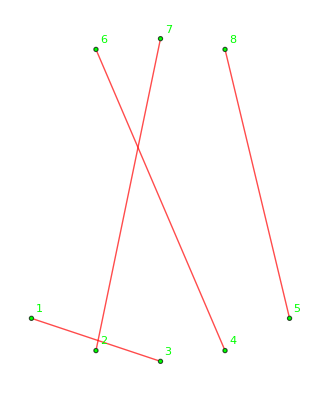
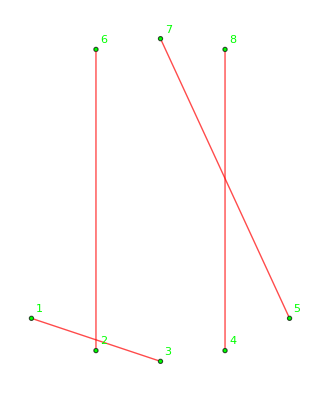
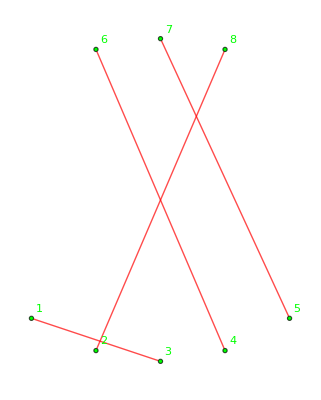
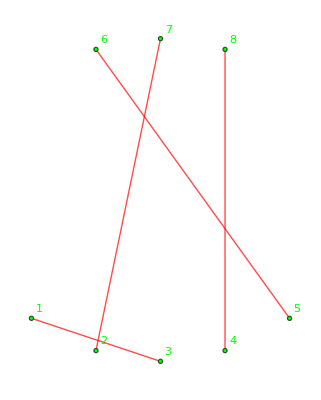
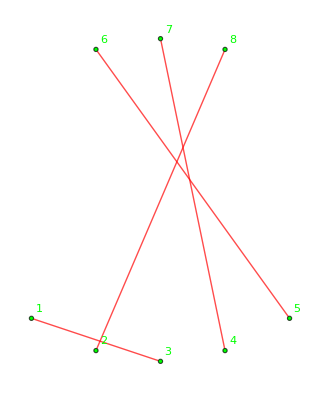
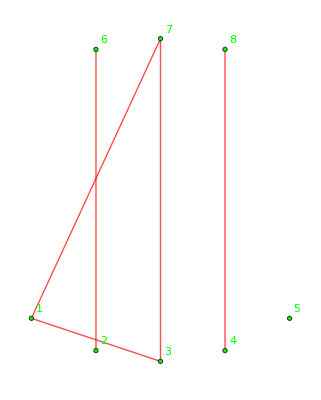
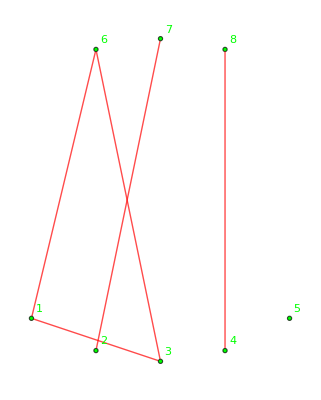
{-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{3,3,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{5,1,1,1}}

```mathematica
ShowForNodesQuad[8,1]
```

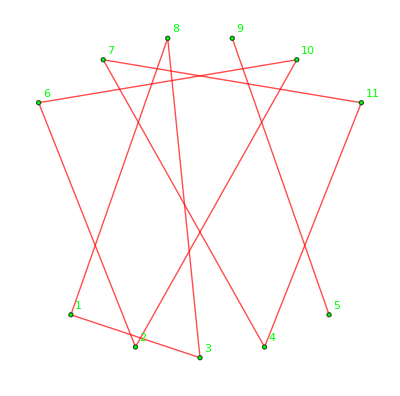
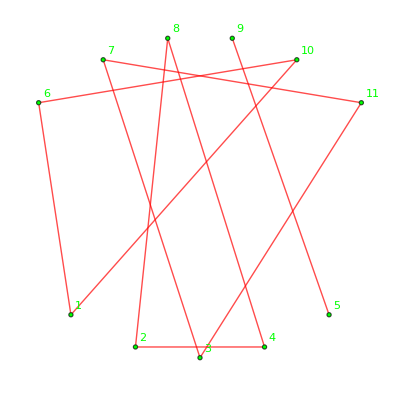
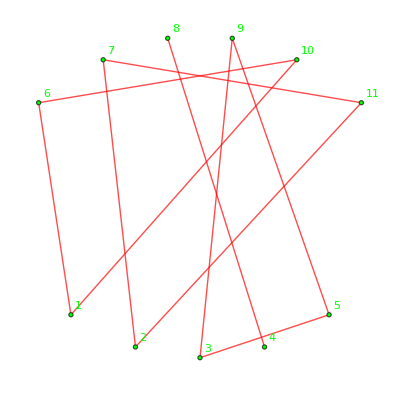
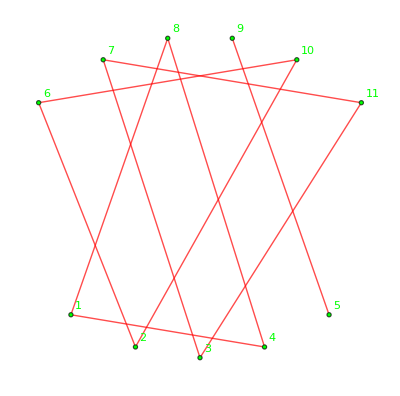
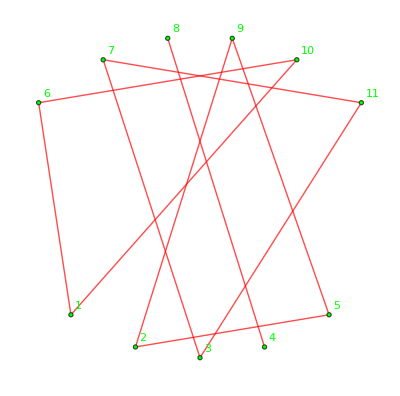
{-Graphics-{3,3,3,2},-Graphics-{3,3,3,2},-Graphics-{3,3,3,2},-Graphics-{3,3,3,2},-Graphics-{3,3,3,2}}

```mathematica
Table[Framed[First[ShowForNodesQuad[11,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

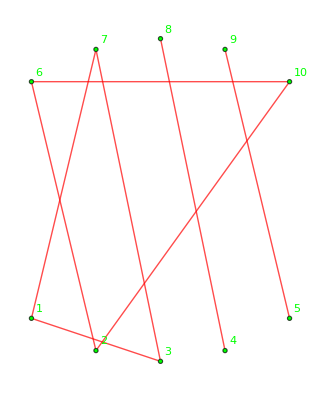
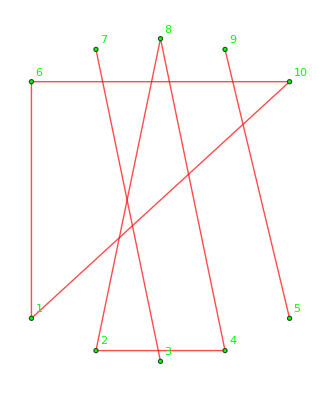
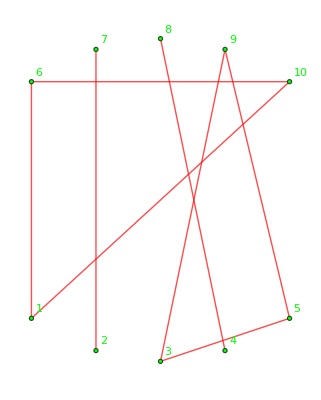
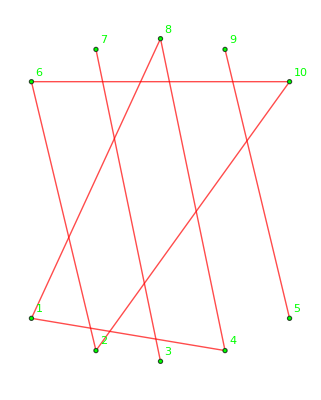
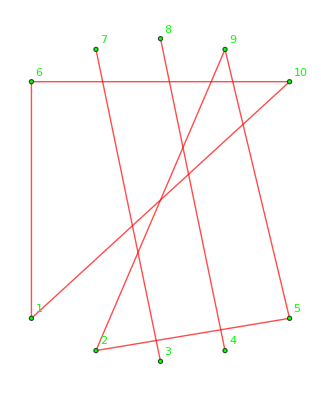
{-Graphics-{3,3,2,2},-Graphics-{3,3,2,2},-Graphics-{3,3,2,2},-Graphics-{3,3,2,2},-Graphics-{3,3,2,2}}

```mathematica
Table[Framed[First[ShowForNodesQuad[10,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

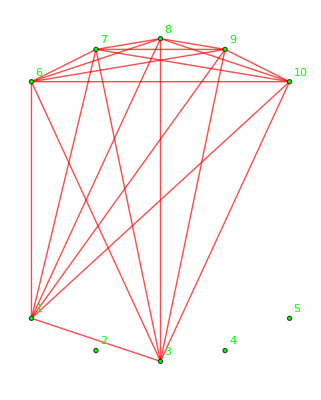
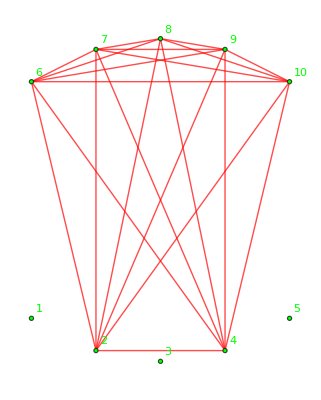
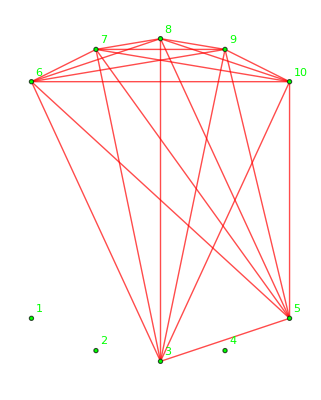
{-Graphics-{7,1,1,1},-Graphics-{7,1,1,1},-Graphics-{7,1,1,1},-Graphics-{7,1,1,1},-Graphics-{7,1,1,1}}

```mathematica
Table[Framed[Last[ShowForNodesQuad[10,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

```mathematica
Table[Framed[First[ShowForNodesQuad[9,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

{-Graphics-{3,2,2,2},-Graphics-{3,2,2,2},-Graphics-{3,2,2,2},-Graphics-{3,2,2,2},-Graphics-{3,2,2,2}}

```mathematica
Table[Framed[Last[ShowForNodesQuad[9,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

{-Graphics-{6,1,1,1},-Graphics-{6,1,1,1},-Graphics-{6,1,1,1},-Graphics-{6,1,1,1},-Graphics-{6,1,1,1}}

```mathematica
Table[Framed[First[ShowForNodesQuad[7,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

{-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{2,2,2,1},-Graphics-{2,2,2,1}}

```mathematica
Table[Framed[First[ShowForNodesQuad[8,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

{-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2},-Graphics-{2,2,2,2}}

```mathematica
Table[Framed[Last[ShowForNodesQuad[8,k]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

{-Graphics-{5,1,1,1},-Graphics-{5,1,1,1},-Graphics-{5,1,1,1},-Graphics-{5,1,1,1},-Graphics-{5,1,1,1}}

```mathematica
Table[Framed[First[RandomSample[ ShowForNodesQuad[8,k]]],FrameStyle->Directive[Darker[Green]//Darker,Thin]],{k,1,5}]
```

{-Graphics-{3,2,2,1},-Graphics-{4,2,1,1},-Graphics-{4,2,1,1},-Graphics-{3,2,2,1},-Graphics-{3,2,2,1}}

```mathematica
Overlay[Table[Last[ShowForNodesQuad[9,k]],{k,1,5}]]
```

-Graphics-{6,1,1,1}-Graphics-{6,1,1,1}-Graphics-{6,1,1,1}-Graphics-{6,1,1,1}-Graphics-{6,1,1,1}

```mathematica
With[{sets=SymbolToSets[v16x247x35x8]},
With[{nodes=Length[Flatten[sets]]},
CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[sets]]},
Join[EdgeList[g],Range[nodes]]],VertexLabels->"Name",VertexCoordinates->CoordinatesForNodes[nodes],GraphHighlightStyle->"Thick"]]
]
```

-Graphics-

```mathematica
With[{sets=SymbolToSets[v13x247x58x6]},
With[{nodes=Length[Flatten[sets]]},
CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[sets]]},
Join[EdgeList[g],Range[nodes]]],GraphHighlightStyle->"Thick",VertexLabels->"Name",VertexCoordinates->CoordinatesForNodes[nodes]]]
]
```

-Graphics-

## Trying to a automate

```mathematica
Clear[ShowForNodesFull];ShowForNodesFull[nodes_,operation_:First]:=Block[
{
part1=operation[QuadrilateralsWithPattern[nodes,1]],
part2=operation[QuadrilateralsWithPattern[nodes,2]],
part3=operation[QuadrilateralsWithPattern[nodes,3]],
part4=operation[QuadrilateralsWithPattern[nodes,4]],
part5=operation[QuadrilateralsWithPattern[nodes,5]]
},
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]]
},
{Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]], SymbolLevel[#]==4&],{part1,part2,part3,part4,part5}}
]
]
```

```mathematica
ShowForNodesFull[7,First]
```

{{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}},{{1,6},{2,7},{3,5},{4}},{{1,4},{2,6},{3,7},{5}},{{1,6},{2,5},{3,7},{4}}}

{{v1x26x35x47,v1x247x35x6,v16x2x35x47,v16x27x35x4,v16x25x3x47,v16x25x37x4,v16x247x3x5,v16x24x37x5,v16x24x35x7,v14x27x35x6,v14x26x37x5,v14x26x35x7,v14x25x37x6,v13x26x47x5,v13x25x47x6,v13x247x5x6},{{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}},{{1,6},{2,7},{3,5},{4}},{{1,4},{2,6},{3,7},{5}},{{1,6},{2,5},{3,7},{4}}}}

```mathematica
GraphFromSymbol[s_]:=With[{sets=SymbolToSets[s]},
With[{nodes=Length[Flatten[sets]]},
CompleteGraph[nodes,GraphHighlight->With[{g=GraphComplement[GraphFromSets[sets]]},
Join[EdgeList[g],Range[nodes]]],GraphHighlightStyle->"Thick",VertexLabels->"Name",VertexCoordinates->CoordinatesForNodes[nodes],ImageSize->150,EdgeStyle->Thin]]
]
```

```mathematica
Table[Map[With[{sym=SymbolToSets[#]},Labeled[Framed[GraphFromSymbol[#],FrameStyle->If[MemberQ[sol[[2]],sym],Directive[Dotted,Thick,Orange],If[HasQuadrilateralPattern[sym],Red,Green//Darker]]],SetsToLabel2[sym]]]&,sol[[1]]],{sol,{ShowForNodesFull[7,First]}}]
```

{{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}},{{1,6},{2,7},{3,5},{4}},{{1,4},{2,6},{3,7},{5}},{{1,6},{2,5},{3,7},{4}}}

{{-Graphics-26♁35♁47,-Graphics-247♁35,-Graphics-16♁35♁47,-Graphics-16♁27♁35,-Graphics-16♁25♁47,-Graphics-16♁25♁37,-Graphics-16♁247,-Graphics-16♁24♁37,-Graphics-16♁24♁35,-Graphics-14♁27♁35,-Graphics-14♁26♁37,-Graphics-14♁26♁35,-Graphics-14♁25♁37,-Graphics-13♁26♁47,-Graphics-13♁25♁47,-Graphics-13♁247}}